```mathematica
Genus Two Minesweeper
```

By: Kaaustaaub Shankar and Matthew Pimienta
An actual implementation of double torus Minesweeper which we will use to perform queries for the solver.

```mathematica
numOfRows=11
```

11

### Play

```mathematica
(*Evaluate all the cells and run the segment below to run the game
If you wish to use the randomize button and sliders under them, make sure that the mineDensity * 8*numOfRows^2 is an integer*)
sector = 1;
row = 1;
column = 1;
numOfRows = 8;
initGame[numOfRows,288,{sector,row,column}];
sectionLst = {};
```

```mathematica
play[board,boardGraphics]
```

Flags Left: 
Revealed Tiles: 

Randomize
{,Rows: }
{,Number of Mines: }
{,Sector Clicked: }
{,Row Clicked: }
{,Tile Clicked: }

### Using the Solver

```mathematica
?autoSolve
```

```mathematica
autoSolve[solverInterface,moreEfficientHeur]
```

Guessing

Mine

Guessing

Mine

{{1},{{1},6,{1}},1,{{{{EdgeForm[{Thickness[Large],GrayLevel[0]}],{RGBColor[0, 0, 1],Triangle[{{-0.382683,0.92388},{0.,0.},{0.382683,0.92388}}]},Text[0,{0.,0.61592}]}},{1},9,{{EdgeForm[{Thickness[Large],GrayLevel[0]}],{GrayLevel[0.5],Triangle[{{-4.5922,11.0866},{-4.20952,10.1627},{-3.82683,11.0866}}]},Text[,{-4.20952,10.7786}]},{EdgeForm[{Thickness[Large],GrayLevel[0]}],{GrayLevel[0.5],Triangle[{{-4.20952,10.1627},{-3.82683,11.0866},{-3.44415,10.1627}}]},Text[,{-3.82683,10.4706}]},19,{EdgeForm[{Thickness[Large],GrayLevel[0]}],{GrayLevel[0.5],Triangle[{{3.44415,10.1627},{3.82683,11.0866},{4.20952,10.1627}}]},Text[,{3.82683,10.4706}]},{EdgeForm[{Thickness[Large],GrayLevel[0]}],{GrayLevel[0.5],Triangle[{{3.82683,11.0866},{4.20952,10.1627},{4.5922,11.0866}}]},Text[,{4.20952,10.7786}]}}},6,{1}}}
 |  |  |  |

```mathematica
solverInterface=initSolver[numOfRows];
```

Before

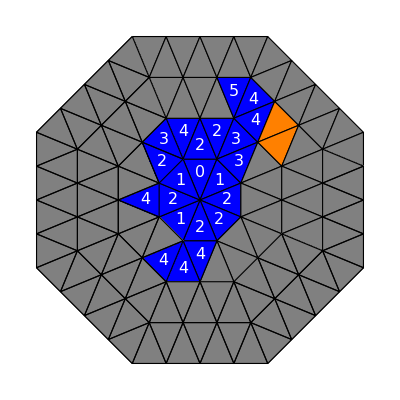

Guessing

Mine

After

-Graphics-

19.508302

```mathematica
(*One step of the solver*)
start=AbsoluteTime[];
Print["Before"];
Graphics[displayBoard[board]]
interfaceNext[solverInterface,moreEfficientHeur,True];
Print["After"];
Graphics[displayBoard[board]]
Print[AbsoluteTime[]-start]
```

```mathematica
boardifyFlatIndex[118,4]
```

{8,3,2}

```mathematica
boardifyFlatIndex[70,4]
```

{5,3,2}

```mathematica
board⟦8,3,2,MINETYPEI⟧
```

0

### Setting Up Board

#### Global variables

Indexing

```mathematica
MINETYPEI=1;
REVEALORNOT = 2;
NEIGHBORDATAI=3;
TRIPOINTI=4;
NMINESI=5;
ISFLAGGEDI = 6;
```

Mine and other attributes

```mathematica
MINE = 1;
NOTMINE = 0;
NOTREVEALED = 0;
REVEALED = 1;
ISFLAGGED = True;
NOTFLAGGED = False;
```

#### Getters

```mathematica
(*Returns whether all unmines have been revealed*)
isComplete[board_]:=
Module[
{completed=True},
Do[
If[tile⟦REVEALORNOT⟧==NOTREVEALED&&tile⟦MINETYPEI⟧==NOTMINE,completed=False;Break[]]
,{sector,board}
,{row,sector}
,{tile,row}
];
Return[completed]
]
```

#### Mine setup

```mathematica
(*Returns neighbors which have no omines*)
neighborsWith0[board_, section_,row_,column_]:=Select[board⟦section,row,column,3⟧,board⟦#⟦1⟧,#⟦2⟧,#⟦3⟧,1⟧===0&&board⟦#⟦1⟧,#⟦2⟧,#⟦3⟧,2⟧===0 &]
```

```mathematica
(*This method returns a board without the primitives, just if its a mine or not*)
setupMines[numOfRows_,numMines_]:= 
Module[
{indicesPlace=RandomSample[Range[8 numOfRows^2]],
currentIndex,
mineLst=Table[NOTMINE,{sector,8},{row,numOfRows},{tile,2row-1}]
},

Do[
currentIndex=boardifyFlatIndex[index,numOfRows];
mineLst⟦currentIndex⟦1⟧,currentIndex⟦2⟧,currentIndex⟦3⟧⟧=MINE;
,{index,indicesPlace}
];

Return [mineLst]
]
```

```mathematica
setupMines[3,0.25]
```

{{{{0,0}},{{0,0},{0,0},{0,0}},{{0,0},{1,0},{0,0},{1,0},{0,0}}},{{{0,0}},{{0,0},{0,0},{1,0}},{{1,0},{0,0},{0,0},{0,0},{0,0}}},{{{0,0}},{{0,0},{1,0},{0,0}},{{1,0},{0,0},{0,0},{0,0},{1,0}}},{{{1,0}},{{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0}}},{{{0,0}},{{0,0},{0,0},{0,0}},{{1,0},{1,0},{0,0},{0,0},{0,0}}},{{{0,0}},{{0,0},{0,0},{0,0}},{{0,0},{0,0},{1,0},{0,0},{0,0}}},{{{1,0}},{{1,0},{1,0},{1,0}},{{0,0},{0,0},{0,0},{1,0},{0,0}}},{{{0,0}},{{1,0},{1,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0}}}}

```mathematica
(*This method returns a board without the primitives, just if its a mine or not*)
setupMines[numOfRows_,numMines_,offLimits_]:= 
Module[
{indicesPlace=RandomSample[Table[If[!MemberQ[offLimits,boardifyFlatIndex[i,numOfRows]],i,Nothing],{i,8 numOfRows^2}],numMines],
currentIndex,
mineLst=Table[NOTMINE,{sector,8},{row,numOfRows},{tile,2row-1}]
},

Do[
currentIndex=boardifyFlatIndex[index,numOfRows];
mineLst⟦currentIndex⟦1⟧,currentIndex⟦2⟧,currentIndex⟦3⟧⟧=MINE;
,{index,indicesPlace}
];

Return [mineLst]
]
```

```mathematica
Table[0,{x,8},{y,8},{z,8}]
```

{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}}

#### Triangle point setup

Setting up coordinates of triangles.

```mathematica
(*Construct a single row of triangles for the tiling*)
constructTiledTriangleRow[numItems_,offset_]:=Module[
{(*This constructs the zigzag shape of the triangles*)
zigzag=Riffle[
Table[N@{pointX,Sin[(3π)/8]}+offset,{pointX,-(numItems+1)/2 Cos[(3π)/8],(numItems+1)/2 Cos[(3π)/8],2Cos[(3π)/8]}],
Table[N@{pointX,0}+offset,{pointX,-(numItems-1)/2 Cos[(3π)/8],(numItems-1)/2 Cos[(3π)/8],2Cos[(3π)/8]}]

]
},
(*Take advantage of the zigzag shape to construct triangles*)
Return[Table[{zigzag⟦i⟧,zigzag⟦i+1⟧,zigzag⟦i+2⟧},{i,numItems}]]
]
```

```mathematica
constructTiledTriangleRow[5,{0,0}]
```

{{{-1.14805,0.92388},{-0.765367,0.},{-0.382683,0.92388}},{{-0.765367,0.},{-0.382683,0.92388},{0.,0.}},{{-0.382683,0.92388},{0.,0.},{0.382683,0.92388}},{{0.,0.},{0.382683,0.92388},{0.765367,0.}},{{0.382683,0.92388},{0.765367,0.},{1.14805,0.92388}}}

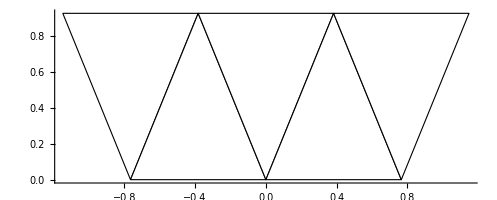

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[constructTiledTriangleRow[5,{0,0}]]},Axes->True]
```

```mathematica
(*Constructs a "big" triangle*)
constructTiledTriangle[numRows_]:=Table[constructTiledTriangleRow[numTriangles,{0,(numTriangles-1)/2*Sin[(3π)/8]}],{numTriangles,1,2numRows-1,2}]
```

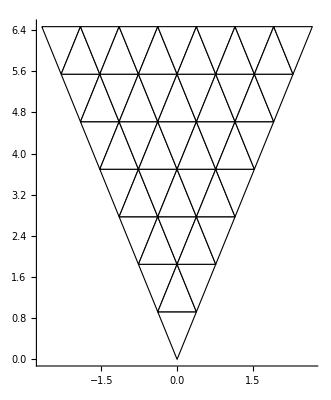

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[Join@@constructTiledTriangle[7]]},Axes->True]
```

```mathematica
(*Rotate points of a triangle created from constructTiledTriangle*)
rotateMassTriangle[triangles_,θ_]:=Table[Table[Table[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.point,{point,triangle}],{triangle,row}],{row,triangles}]
```

```mathematica
(*Construct triangle points for the board tiles.
The return structure is structured the same way as a regular board, except this only gives tile corner coordinates
*)
createBoardSkeleton[numRows_]:=Table[rotateMassTriangle[constructTiledTriangle[numRows],θ],{θ,2π,π/4,-π/4}]
```

```mathematica
createBoardSkeleton[3]
```

{{{{{-0.382683,0.92388},{0.,0.},{0.382683,0.92388}}},{{{-0.765367,1.84776},{-0.382683,0.92388},{0.,1.84776}},{{-0.382683,0.92388},{0.,1.84776},{0.382683,0.92388}},{{0.,1.84776},{0.382683,0.92388},{0.765367,1.84776}}},{{{-1.14805,2.77164},{-0.765367,1.84776},{-0.382683,2.77164}},{{-0.765367,1.84776},{-0.382683,2.77164},{0.,1.84776}},{{-0.382683,2.77164},{0.,1.84776},{0.382683,2.77164}},{{0.,1.84776},{0.382683,2.77164},{0.765367,1.84776}},{{0.382683,2.77164},{0.765367,1.84776},{1.14805,2.77164}}}},{{{{0.382683,0.92388},{0.,0.},{0.92388,0.382683}}},{{{0.765367,1.84776},{0.382683,0.92388},{1.30656,1.30656}},{{0.382683,0.92388},{1.30656,1.30656},{0.92388,0.382683}},{{1.30656,1.30656},{0.92388,0.382683},{1.84776,0.765367}}},{{{1.14805,2.77164},{0.765367,1.84776},{1.68925,2.23044}},{{0.765367,1.84776},{1.68925,2.23044},{1.30656,1.30656}},{{1.68925,2.23044},{1.30656,1.30656},{2.23044,1.68925}},{{1.30656,1.30656},{2.23044,1.68925},{1.84776,0.765367}},{{2.23044,1.68925},{1.84776,0.765367},{2.77164,1.14805}}}},{{{{0.92388,0.382683},{0.,0.},{0.92388,-0.382683}}},{{{1.84776,0.765367},{0.92388,0.382683},{1.84776,0.}},{{0.92388,0.382683},{1.84776,0.},{0.92388,-0.382683}},{{1.84776,0.},{0.92388,-0.382683},{1.84776,-0.765367}}},{{{2.77164,1.14805},{1.84776,0.765367},{2.77164,0.382683}},{{1.84776,0.765367},{2.77164,0.382683},{1.84776,0.}},{{2.77164,0.382683},{1.84776,0.},{2.77164,-0.382683}},{{1.84776,0.},{2.77164,-0.382683},{1.84776,-0.765367}},{{2.77164,-0.382683},{1.84776,-0.765367},{2.77164,-1.14805}}}},{{{{0.92388,-0.382683},{0.,0.},{0.382683,-0.92388}}},{{{1.84776,-0.765367},{0.92388,-0.382683},{1.30656,-1.30656}},{{0.92388,-0.382683},{1.30656,-1.30656},{0.382683,-0.92388}},{{1.30656,-1.30656},{0.382683,-0.92388},{0.765367,-1.84776}}},{{{2.77164,-1.14805},{1.84776,-0.765367},{2.23044,-1.68925}},{{1.84776,-0.765367},{2.23044,-1.68925},{1.30656,-1.30656}},{{2.23044,-1.68925},{1.30656,-1.30656},{1.68925,-2.23044}},{{1.30656,-1.30656},{1.68925,-2.23044},{0.765367,-1.84776}},{{1.68925,-2.23044},{0.765367,-1.84776},{1.14805,-2.77164}}}},{{{{0.382683,-0.92388},{0.,0.},{-0.382683,-0.92388}}},{{{0.765367,-1.84776},{0.382683,-0.92388},{0.,-1.84776}},{{0.382683,-0.92388},{0.,-1.84776},{-0.382683,-0.92388}},{{0.,-1.84776},{-0.382683,-0.92388},{-0.765367,-1.84776}}},{{{1.14805,-2.77164},{0.765367,-1.84776},{0.382683,-2.77164}},{{0.765367,-1.84776},{0.382683,-2.77164},{0.,-1.84776}},{{0.382683,-2.77164},{0.,-1.84776},{-0.382683,-2.77164}},{{0.,-1.84776},{-0.382683,-2.77164},{-0.765367,-1.84776}},{{-0.382683,-2.77164},{-0.765367,-1.84776},{-1.14805,-2.77164}}}},{{{{-0.382683,-0.92388},{0.,0.},{-0.92388,-0.382683}}},{{{-0.765367,-1.84776},{-0.382683,-0.92388},{-1.30656,-1.30656}},{{-0.382683,-0.92388},{-1.30656,-1.30656},{-0.92388,-0.382683}},{{-1.30656,-1.30656},{-0.92388,-0.382683},{-1.84776,-0.765367}}},{{{-1.14805,-2.77164},{-0.765367,-1.84776},{-1.68925,-2.23044}},{{-0.765367,-1.84776},{-1.68925,-2.23044},{-1.30656,-1.30656}},{{-1.68925,-2.23044},{-1.30656,-1.30656},{-2.23044,-1.68925}},{{-1.30656,-1.30656},{-2.23044,-1.68925},{-1.84776,-0.765367}},{{-2.23044,-1.68925},{-1.84776,-0.765367},{-2.77164,-1.14805}}}},{{{{-0.92388,-0.382683},{0.,0.},{-0.92388,0.382683}}},{{{-1.84776,-0.765367},{-0.92388,-0.382683},{-1.84776,0.}},{{-0.92388,-0.382683},{-1.84776,0.},{-0.92388,0.382683}},{{-1.84776,0.},{-0.92388,0.382683},{-1.84776,0.765367}}},{{{-2.77164,-1.14805},{-1.84776,-0.765367},{-2.77164,-0.382683}},{{-1.84776,-0.765367},{-2.77164,-0.382683},{-1.84776,0.}},{{-2.77164,-0.382683},{-1.84776,0.},{-2.77164,0.382683}},{{-1.84776,0.},{-2.77164,0.382683},{-1.84776,0.765367}},{{-2.77164,0.382683},{-1.84776,0.765367},{-2.77164,1.14805}}}},{{{{-0.92388,0.382683},{0.,0.},{-0.382683,0.92388}}},{{{-1.84776,0.765367},{-0.92388,0.382683},{-1.30656,1.30656}},{{-0.92388,0.382683},{-1.30656,1.30656},{-0.382683,0.92388}},{{-1.30656,1.30656},{-0.382683,0.92388},{-0.765367,1.84776}}},{{{-2.77164,1.14805},{-1.84776,0.765367},{-2.23044,1.68925}},{{-1.84776,0.765367},{-2.23044,1.68925},{-1.30656,1.30656}},{{-2.23044,1.68925},{-1.30656,1.30656},{-1.68925,2.23044}},{{-1.30656,1.30656},{-1.68925,2.23044},{-0.765367,1.84776}},{{-1.68925,2.23044},{-0.765367,1.84776},{-1.14805,2.77164}}}}}

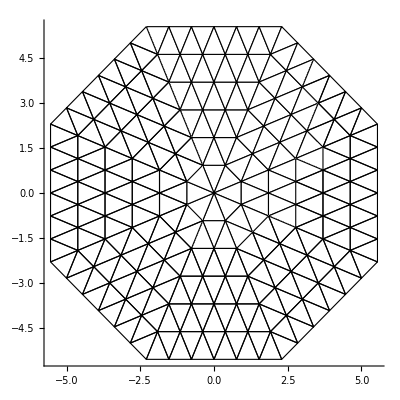

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[Join@@Join@@createBoardSkeleton[6]]},Axes->True]
```

#### Neighbors setup (point comparison)

We use an association to figure out which triangles share points. The coordinates will be rounded by a 1/100 to accommodate a reasonable floating point error.
We then handle adjacencies by outer edge connection as a separate case

```mathematica
(*Error checking to ensure we do not add any invalid neighbors. Less cases to handle manually*)
SetAttributes[addNeighbor,HoldFirst]
addNeighbor[neighborLst_,numRows_,sector_,row_,tile_]:=
If[1≤sector≤8&&1≤row≤numRows&&1≤tile≤2*row-1&&!MemberQ[neighborLst,{sector,row,tile}],AppendTo[neighborLst,{sector,row,tile}]
]
```

```mathematica
roundCoordHundredths[coord_]:=Map[Round[#*100]/100.&,coord]
```

```mathematica
(*Returns an association. Each key is a point rounded to the hundredths, and the values are lists of triangles which have that point*)
findSharedPoints[trianglesCoords_]:=
Module[{pointsAssociations=Association[]},

Do[
(*Point is not yet in association*)
If[MissingQ@pointsAssociations[roundCoordHundredths[point]],
AssociateTo[pointsAssociations,roundCoordHundredths[point]->{}];
];
(*Add point to association*)
AssociateTo[pointsAssociations,roundCoordHundredths[point]->Append[pointsAssociations[roundCoordHundredths[point]],{sectorI,rowI,tileI}]];
,{sectorI,Length@trianglesCoords}
,{rowI,Length@trianglesCoords⟦sectorI⟧}
,{tileI,Length@trianglesCoords⟦sectorI,rowI⟧}
,{point,trianglesCoords⟦sectorI,rowI,tileI⟧}
];
Return[pointsAssociations]
]
```

```mathematica
(*Returns the number of mines around this tile*)
countMines[mineLst_,neighborLst_,sector_,row_,tile_]:=Module[
{},
Return[Length@Select[neighborLst⟦sector,row,tile,1⟧,mineLst⟦#⟦1⟧,#⟦2⟧,#⟦3⟧⟧==1&]]
]
```

```mathematica
(*Returns the neighbors of each tile in the tiling given the coordinates of the tiles.
Returns in the same form as the regular board, but only giving the neighbor data.
*)
setupNeighbors[mineLst_,trianglesCoords_]:=
Module[
{pointsSharing=findSharedPoints[trianglesCoords],
neighborLst=Table[Table[Table[{{}},{tile,row}],{row,sector}],{sector,trianglesCoords}],
POI,
countMinesLst
},
POI=Keys[pointsSharing];
(*Add adjacent triangles*)
Do[
If[triangle1==triangle2||
MemberQ[neighborLst⟦triangle1⟦1⟧,triangle1⟦2⟧,triangle1⟦3⟧,1⟧,triangle2]||
mineLst⟦triangle1⟦1⟧,triangle1⟦2⟧,triangle1⟦3⟧⟧,Continue[]];
AppendTo[neighborLst⟦triangle1⟦1⟧,triangle1⟦2⟧,triangle1⟦3⟧,1⟧,triangle2];
,{point,POI}
,{triangle1,pointsSharing[point]}
,{triangle2,pointsSharing[point]}
];
setupNeighborsConnectEdges[neighborLst];
(*All vertices of octagon coincide into a point*)
Do[
If[{sector,tile}=={otherSector,otherTile},Continue[]];
AppendTo[neighborLst⟦sector,Length@mineLst⟦1⟧,tile,1⟧,{otherSector,Length@mineLst⟦1⟧,otherTile}]
,{sector,Length@mineLst}
,{tile,{1,2Length@mineLst⟦sector⟧-1}}
,{otherSector,Length@mineLst}
,{otherTile,{1,2Length@mineLst⟦otherSector⟧-1}}
];
(*Count mines around tiles*)
Do[
neighborLst⟦sector,row,tile,1⟧=DeleteDuplicates[neighborLst⟦sector,row,tile,1⟧];
AppendTo[neighborLst⟦sector,row,tile⟧,countMines[mineLst,neighborLst,sector,row,tile]]
,{sector,Length@neighborLst}
,{row,Length@neighborLst⟦sector⟧}
,{tile,Length@neighborLst⟦sector,row⟧}
];
Return[neighborLst];
]
```

```mathematica
SetAttributes[setupNeighborsConnectEdges,HoldFirst]
(*Performs octagon edge connection with setting up adjacencies*)
setupNeighborsConnectEdges[existingLst_]:=Module[
{},
setupNeighborsConnectSectorPairs[existingLst,1,3];
setupNeighborsConnectSectorPairs[existingLst,2,4];
setupNeighborsConnectSectorPairs[existingLst,5,7];
setupNeighborsConnectSectorPairs[existingLst,6,8];
setupNeighborsConnectSectorPairs[existingLst,3,1];
setupNeighborsConnectSectorPairs[existingLst,4,2];
setupNeighborsConnectSectorPairs[existingLst,7,5];
setupNeighborsConnectSectorPairs[existingLst,8,6];

]
```

```mathematica
SetAttributes[setupNeighborsConnectSectorPairs,HoldFirst]
(*Connect edges of octagon via neighbor pairings*)
setupNeighborsConnectSectorPairs[existingLst_,sector_,otherSector_]:=Module[
{numRows=Length@existingLst⟦1⟧,tile},
(*"up" pointing triangles*)
Do[
addNeighbor[existingLst⟦sector,numRows,tile,1⟧,numRows,otherSector,numRows,otherTile]
,{tile,2,2numRows-2,2}
,{otherTile,2numRows-tile-1,2numRows-tile+1}
];
(*"Down" pointing triangles*)
Do[
addNeighbor[existingLst⟦sector,numRows,tile,1⟧,numRows,otherSector,numRows,otherTile]
,{tile,1,2numRows-1,2}
,{otherTile,2numRows-tile-2,2numRows-tile+2}
];
]
```

```mathematica
bb=setupNeighbors[setupMines[3,0.25],createBoardSkeleton[2]]
```

{{{{{{1,2,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{1,2,3},{2,2,1},{2,2,2}},0}},{{{{1,1,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3},{1,2,3}},1},{{{1,1,1},{1,2,1},{8,1,1},{8,2,2},{8,2,3},{1,2,3},{2,1,1},{2,2,1},{2,2,2}},1},{{{1,1,1},{1,2,2},{2,1,1},{2,2,1},{2,2,2},{1,2,1}},1}}},{{{{{1,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{1,2,2},{1,2,3},{2,2,1},{2,2,2},{2,2,3},{3,2,1},{3,2,2}},3}},{{{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,2},{2,2,3}},1},{{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,1},{2,2,3},{3,1,1},{3,2,1},{3,2,2}},2},{{{2,1,1},{2,2,2},{3,1,1},{3,2,1},{3,2,2},{2,2,1}},1}}},{{{{{1,1,1},{2,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{2,2,2},{2,2,3},{3,2,1},{3,2,2},{3,2,3},{4,2,1},{4,2,2}},0}},{{{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,2},{3,2,3}},2},{{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,1},{3,2,3},{4,1,1},{4,2,1},{4,2,2}},3},{{{3,1,1},{3,2,2},{4,1,1},{4,2,1},{4,2,2},{3,2,1}},0}}},{{{{{1,1,1},{2,1,1},{3,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{3,2,2},{3,2,3},{4,2,1},{4,2,2},{4,2,3},{5,2,1},{5,2,2}},5}},{{{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,2},{4,2,3}},0},{{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,1},{4,2,3},{5,1,1},{5,2,1},{5,2,2}},3},{{{4,1,1},{4,2,2},{5,1,1},{5,2,1},{5,2,2},{4,2,1}},1}}},{{{{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{6,1,1},{7,1,1},{8,1,1},{4,2,2},{4,2,3},{5,2,1},{5,2,2},{5,2,3},{6,2,1},{6,2,2}},5}},{{{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,2},{5,2,3}},0},{{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,1},{5,2,3},{6,1,1},{6,2,1},{6,2,2}},3},{{{5,1,1},{5,2,2},{6,1,1},{6,2,1},{6,2,2},{5,2,1}},3}}},{{{{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{7,1,1},{8,1,1},{5,2,2},{5,2,3},{6,2,1},{6,2,2},{6,2,3},{7,2,1},{7,2,2}},0}},{{{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,2},{6,2,3}},0},{{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,1},{6,2,3},{7,1,1},{7,2,1},{7,2,2}},0},{{{6,1,1},{6,2,2},{7,1,1},{7,2,1},{7,2,2},{6,2,1}},3}}},{{{{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{8,1,1},{6,2,2},{6,2,3},{7,2,1},{7,2,2},{7,2,3},{8,2,1},{8,2,2}},4}},{{{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,2},{7,2,3}},2},{{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,1},{7,2,3},{8,1,1},{8,2,1},{8,2,2}},2},{{{7,1,1},{7,2,2},{8,1,1},{8,2,1},{8,2,2},{7,2,1}},0}}},{{{{{1,1,1},{1,2,1},{1,2,2},{8,2,2},{8,2,3},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{7,2,2},{7,2,3},{8,2,1}},3}},{{{{7,1,1},{7,2,2},{7,2,3},{8,1,1},{8,2,2},{8,2,3}},0},{{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,3},{7,1,1},{7,2,2},{7,2,3},{8,2,1}},1},{{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,2},{8,2,1}},1}}}}

#### display functions

```mathematica
(*Returns graphics primitives to highlight given tiles*)
highlightTiles[tiles_]:=
{EdgeForm[{Thickness[Large],Red}],Red,Opacity[0.5],Table[Triangle[board⟦tile⟦1⟧,tile⟦2⟧,tile⟦3⟧,TRIPOINTI⟧],{tile,tiles}]}
```

```mathematica
(*Displays entire board using table to go through sector row and column*)
displayBoard[board_]:= 
Table[graphicsAtTile[board,sector,row,column],{sector,Length@board},{row,Length@board⟦sector⟧},{column,Length@board⟦sector,row⟧}]
```

```mathematica
(*Display octagonal edge colorings*)
displayBoardConnections[board_]:={
Thickness[0.01],Red,Arrow[(Length@board⟦1⟧+0.5)*{{{Cos[3π/8],Sin[3π/8]},{Cos[5π/8],Sin[5π/8]}},{{Cos[π/8],Sin[π/8]},{Cos[-π/8],Sin[-π/8]}}}],
Thickness[0.01],Blue,Arrow[(Length@board⟦1⟧+0.5)*{{Cos[3π/8],Sin[3π/8]},{Cos[π/8],Sin[π/8]}}],
Thickness[0.01],Blue,Arrow[(Length@board⟦1⟧+0.5)*{{Cos[-3π/8],Sin[-3π/8]},{Cos[-π/8],Sin[-π/8]}}],
Thickness[0.01],Green,Arrow[-(Length@board⟦1⟧+0.5)*{{Cos[π/8],Sin[π/8]},{Cos[3π/8],Sin[3π/8]}}],
Thickness[0.01],Green,Arrow[-(Length@board⟦1⟧+0.5)*{{Cos[-π/8],Sin[-π/8]},{Cos[-3π/8],Sin[-3π/8]}}],
Thickness[0.01],Purple,Arrow[-(Length@board⟦1⟧+0.5)*{{{Cos[3π/8],Sin[3π/8]},{Cos[5π/8],Sin[5π/8]}},{{Cos[π/8],Sin[π/8]},{Cos[-π/8],Sin[-π/8]}}}]
}
```

```mathematica
(*Graphics for each tile. checks if mine and if revealed and based off of that, you have text and color*)
graphicsAtTile[board_,sector_,row_,column_]:=Module[
	{tile = board⟦sector,row,column⟧},
		{
		EdgeForm[{Thickness[Large],Black}],{colorAtTile[board,sector,row,column],Triangle[tile⟦TRIPOINTI⟧]},
		If[tile⟦REVEALORNOT⟧==REVEALED,Text[Style[tile⟦NMINESI⟧,FontSize->16,FontColor->White],triangleCentroid[tile⟦TRIPOINTI⟧]],Text["",triangleCentroid[tile⟦TRIPOINTI⟧]]]
		}
]
```

```mathematica
(*Determins what color a certain tile should be*)
colorAtTile[board_,sector_,row_,column_]:= Module[
{tile = board⟦sector,row,column⟧},
	If[tile⟦REVEALORNOT⟧==REVEALED,
		If[tile⟦MINETYPEI⟧ == MINE,
			Return[Red],
			Return[Blue]
		]
		,
		If[tile⟦ISFLAGGEDI⟧ == ISFLAGGED,
			Return[Orange],
			Return[Gray]
		]
	]
]
```

#### Putting it all together

Combine the data for each tile into a single list.

```mathematica
(*Returns the centroid of the triangle*)
triangleCentroid[triangleCoords_]:=RegionCentroid[Triangle[triangleCoords]]
```

```mathematica
(*Set up board completely*)
boardSetUp[numOfRows_,numMines_,clickedTile_]:=Module[
{minesData=setupMines[numOfRows,0],
triangleCoords=createBoardSkeleton[numOfRows],
neighborData,
minesOffLimits,
curEqVarMap=1
},
(*Set up mines and neighbors*)
neighborData=setupNeighbors[minesData,triangleCoords];
minesOffLimits=Append[neighborData⟦clickedTile⟦1⟧,clickedTile⟦2⟧,clickedTile⟦3⟧,1⟧,clickedTile];
minesData=setupMines[numOfRows,numMines,minesOffLimits];
neighborData=setupNeighbors[minesData,triangleCoords];
(*Put everything together in a nested table*)
Return[
Table[
{minesData⟦sectorI,rowI,tileI⟧,
NOTREVEALED,
neighborData⟦sectorI,rowI,tileI,1⟧,
triangleCoords⟦sectorI,rowI,tileI⟧,
If[minesData⟦sectorI⟧⟦rowI⟧⟦tileI⟧ == 0,neighborData⟦sectorI,rowI,tileI,2⟧,""],
NOTFLAGGED
},{sectorI,1,8},{rowI,1,Length@minesData⟦sectorI⟧},{tileI,1,Length@minesData⟦sectorI,rowI⟧}
]
]
]
```

```mathematica
Table[0,{i,5},{f,5}]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

### Interaction With Board

#### More complex operations

```mathematica
(*Initialize game, set up local variables*)
initGame[numRows_,numMines_,startClick_]:=
Module[
{},
flag=numMines;
numOfMines=numMines;
board=boardSetUp[numRows,flag,startClick];
clickType="Reveal";
numRevealedTiles=0;
boardGraphics=displayBoard[board]
]
```

```mathematica
SetAttributes[play,HoldAll]
(*Play game with dynamic stuff*)
play[board_,boardGraphics_]:=
Row[{DynamicModule[{numOfRows,, factor,c = clickType ,sector,row,column,clickTypes = {"Reveal","Flag","Reset"},buttenCount = 0}, 
ClickPane[
	Dynamic[
	(*Display*)
		Graphics[{boardGraphics,displayBoardConnections[board]}, ImageSize->Large]
		],
		(*Interaction*)
	(processClick[sectionLst,board,boardGraphics, triangleAtPoint[#⟦1⟧,#⟦2⟧],clickType])&

	]
	(*Buttons and sliders*)
	],Column[{
	Button[StringForm["Flags Left: `1`",(Dynamic[flag])]],
	Button[StringForm["Revealed Tiles: `1`",Dynamic[numRevealedTiles]]],
	Button[Dynamic[clickType],If[clickType == "Reveal", clickType = "Flag",clickType = "Reveal"]],
	Button["Randomize", initGame[numOfRows,factor,{sector,row,column}]],
	{Slider[Dynamic[numOfRows],{4,10,1}],StringForm["Rows: `1`",Dynamic[numOfRows]]},
	{Slider[Dynamic[factor],{1,Dynamic[8*numOfRows^2],1}],StringForm["Number of Mines: `1`",Dynamic[factor]]},
	{Slider[Dynamic[sector],{1,8,1}],StringForm["Sector Clicked: `1`",Dynamic[sector]]},
	{Slider[Dynamic[row],{1,Dynamic[numOfRows],1}],StringForm["Row Clicked: `1`",Dynamic[row]]},
	{Slider[Dynamic[column],{1,Dynamic[2*numOfRows-1],1}],StringForm["Tile Clicked: `1`",Dynamic[column]]}
	}]}
]
```

```mathematica
SetAttributes[processClick,HoldAll]
(*Handle click from game clickPane*)
processClick[sectionLst_,board_,boardGraphics_,triangle_,flagornot_]:= Module[
	{revealedTiles},
	If[flagornot== "Flag",
		(*Incrementing and decrementing flag count*)
		If[board⟦triangle⟦1⟧,triangle⟦2⟧,triangle⟦3⟧,ISFLAGGEDI⟧, flag++, flag--];
		(*changing whether the falgged status of the tile
		Also changing the graphics for it*)
		board⟦triangle⟦1⟧,triangle⟦2⟧,triangle⟦3⟧,ISFLAGGEDI⟧=!board⟦triangle⟦1⟧,triangle⟦2⟧,triangle⟦3⟧,ISFLAGGEDI⟧;
		boardGraphics⟦triangle⟦1⟧,triangle⟦2⟧,triangle⟦3⟧⟧ = graphicsAtTile[board,triangle⟦1⟧,triangle⟦2⟧,triangle⟦3⟧];
		
		Return[Nothing] 
		,
		If[board⟦triangle⟦1⟧,triangle⟦2⟧,triangle⟦3⟧,REVEALORNOT⟧==REVEALED,Return[{}]];
		revealedTiles = revealTile[board,triangle⟦1⟧,triangle⟦2⟧,triangle⟦3⟧]];
	If[revealedTiles == False,Print["Mine"]; Return[False]];
	numRevealedTiles += Length@DeleteDuplicates[revealedTiles];
	AppendTo[sectionLst,DeleteDuplicates[revealedTiles]];
	Do[
		(*Revealing tiles*)
		board⟦tiles⟦1⟧,tiles⟦2⟧,tiles⟦3⟧,REVEALORNOT⟧ = REVEALED;
		boardGraphics⟦tiles⟦1⟧,tiles⟦2⟧,tiles⟦3⟧⟧ = graphicsAtTile[board,tiles⟦1⟧,tiles⟦2⟧,tiles⟦3⟧]; 

	,{tiles,revealedTiles}];
	Return[revealedTiles]
	
]
```

#### Basic operations

```mathematica
SetAttributes[toggleFlag,HoldFirst]
(*Toggle flag at location*)
toggleFlag[board_,section_,row_,column_]:= board⟦section,row,column,ISFLAGGEDI⟧ = !board⟦section,row,column,ISFLAGGEDI⟧;
```

```mathematica
SetAttributes[revealTile,HoldAll]
(*Reveal tile at location with flood fill*)
revealTile[board_,sector_,row_,tile_]:=Module[
{tileStack={{sector,row,tile}},
allSectors={},
currentTile},
	If[board⟦sector,row,tile,MINETYPEI⟧==MINE,Return[False]];
	
	(*Standard flood fill stuff*)
	While[Length@tileStack>0,
	(*Pop tile and reveal*)
		currentTile=tileStack⟦Length@tileStack⟧;
		tileStack=Delete[tileStack,Length@tileStack];
		board⟦currentTile⟦1⟧,currentTile⟦2⟧,currentTile⟦3⟧,REVEALORNOT⟧=REVEALED;
		(*Add neighbors to stack*)
		If[board⟦currentTile⟦1⟧,currentTile⟦2⟧,currentTile⟦3⟧,NMINESI⟧==0,
			Do[
				If[
					board⟦neighbor⟦1⟧,neighbor⟦2⟧,neighbor⟦3⟧,REVEALORNOT⟧==NOTREVEALED,
					AppendTo[tileStack,neighbor];
					AppendTo[allSectors,neighbor];
					,
					Nothing
				];
			,{neighbor,board⟦currentTile⟦1⟧,currentTile⟦2⟧,currentTile⟦3⟧,NEIGHBORDATAI⟧}
			]
		];
	];
	AppendTo[allSectors,{sector,row,tile}];
	Return[allSectors]
]
```

```mathematica
(*Helper function tofigure out which sector the point is in*)
whichSector[x_,y_]:=Module[
{curPoint={x,y},θ=π/4},
Do[
If[-Cot[(3π)/8]curPoint⟦2⟧<curPoint⟦1⟧<Cot[(3π)/8]curPoint⟦2⟧,Return[i]];
curPoint={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.curPoint
,{i,1,8}
]
]
```

```mathematica
(*Helper function to figure out which tile the point is in given the row*)
findTile[row_,point_]:=Module[
{tempPoint=point+{(row-1)*Cos[3π/8],-(row-1)Sin[(3π)/8]},
checkerEq=ArcCos[Cos[(x)(π/Cos[3π/8])]]*Sin[3π/8]/π},
If[tempPoint⟦2⟧<checkerEq/.{x->tempPoint⟦1⟧},(*Pointing up triangle*)
Return[2*Ceiling[tempPoint⟦1⟧/(2Cos[3π/8])]];
,(*Pointing down triangle*)
Return[2*Round[tempPoint⟦1⟧/(2Cos[3π/8])]+1];
]
]
```

```mathematica
(*Return the index of the triangle at the given point in the graphics*)
triangleAtPoint[x_,y_]:=Module[
{sector=whichSector[x,y],
row,tile,
checkPoint,θ=π/4},
checkPoint={{Cos[(sector-1)θ],-Sin[(sector-1)θ]},{Sin[(sector-1)θ],Cos[(sector-1)θ]}}.{x,y};
row=Ceiling[checkPoint⟦2⟧*Csc[(3π)/8]];
tile=findTile[row,checkPoint];
Return[{sector,row,tile}]
]
```

### Solver

#### Query

```mathematica
(*Global Variables for indexing*)
QUEREVEALTILE=0;
QUETOGGLEFLAG=1;
QUETILETYPE=2;
QUEGETNEIGHBORS=3;
QUERYGRAPHICS=4;
QUERYCOMPLETE=5;
QUEMINESLEFT=6;
```

```mathematica
queryNumMines[input_]:=numOfMines
```

```mathematica
(*Method to allow solver indirect access to the board*)
queryReveal[input_]:=revealTile[board,input⟦2⟧,input⟦3⟧,input⟦4⟧]
```

```mathematica
(*Method to allow solver indirect access to the board*)
queryToggleFlag[input_]:=toggleFlag[board,input⟦2⟧,input⟦3⟧,input⟦4⟧]
```

```mathematica
(*Method to allow solver indirect access to the board*)
queryReveal[input_]:=processClick[sectionLst,board,boardGraphics,{input⟦2⟧,input⟦3⟧,input⟦4⟧},"Reveal"]
```

```mathematica
(*Method to allow solver indirect acces to the board*)
queryToggleFlag[input_]:=processClick[sectionLst,board,boardGraphics,{input⟦2⟧,input⟦3⟧,input⟦4⟧},"Flag"]
```

```mathematica
(*Method to allow solver indirect access to the board*)
queryTileType[input_]:=
Which[
board⟦input⟦2⟧,input⟦3⟧,input⟦4⟧,ISFLAGGEDI⟧==ISFLAGGED,{MINE,1},
board⟦input⟦2⟧,input⟦3⟧,input⟦4⟧,REVEALORNOT⟧==REVEALED,{NOTMINE,board⟦input⟦2⟧,input⟦3⟧,input⟦4⟧,NMINESI⟧},
True,-1
]
```

```mathematica
(*Method to allow solver indirect access to the board*)
queryNeighbors[input_]:=board⟦input⟦2⟧,input⟦3⟧,input⟦4⟧,NEIGHBORDATAI⟧
```

```mathematica
(*Method to allow solver indirect access to the board*)
queryGetDisplay[input_]:=displayBoard[board]
```

```mathematica
(*Method to allow solver indirect access to the board*)
queryIsComplete[input_]:=isComplete[board]
```

```mathematica
(*Perform query on board. Can be updated as needed, but it must implement:
* queryReveal[] - Needs an input of form {QUEREVEALTILE,sector, row, tile}. Return the output of revealTile[] and perform the operation on the given board
* queryToggleFlag[] - Needs an input of form {QUETOGGLEFLAG, sector, row, tile}. Turn on or off the flag and don't output anything
* queryTileType[] - Needs an input of form {QUETILETYPE, sector,row,tile}. Returns a number representing the tile, a -1 being unknown, 0 being revealed, and 1 being a flag.
* queryNeighbors - Needs an input of form {QUEGETNEIGHBORS, sector, row, tile}. Returns a list of board indices of the neighbors at the given tile
* queryGraphics - Needs an input of form {QUERYGRAPHCS}. Returns the graphics of the board
* queryIsComplete - Needs an input of form {QUERYCOMPLETE}. Returns whether or not the board is complete.
*)
SetAttributes[queryBoard,HoldFirst]
queryBoard[input_]:=
Switch[input⟦1⟧,
QUEREVEALTILE,
Return[queryReveal[input]],
QUETOGGLEFLAG,
queryToggleFlag[input],
QUETILETYPE,
Return[queryTileType[input]],
QUEGETNEIGHBORS,
Return[queryNeighbors[input]],
QUERYGRAPHICS,
Return[queryGetDisplay[input]],
QUERYCOMPLETE,
Return[queryIsComplete[input]]
]
```

#### HelperFunctions

```mathematica
(*Convert from board to flat index*)
flattenBoardIndex[index_,numRows_]:=
(*Add sector*)
(index⟦1⟧-1)numRows^2+
(*Add row*)
(index⟦2⟧-1)^2+
(*Add tile*)
index⟦3⟧
```

```mathematica
(*Convert from flat to board index*)
boardifyFlatIndex[index_,numRows_]:=
Module[
{sector=Ceiling[index/numRows^2],
row=Ceiling[Sqrt[Mod[index-1,(numRows^2)]+1]]},
Return[{sector,row,index-(sector-1)numRows^2-(row-1)^2}]
]
```

```mathematica
(*If this is revealed and is next to an unknown tile*)
onBorder[index_,numRows_]:=unknownAround[boardifyFlatIndex[index,numRows]]&&
(queryBoard[Prepend[boardifyFlatIndex[index,numRows],QUETILETYPE]]=!=-1&&queryBoard[Prepend[boardifyFlatIndex[index,numRows],QUETILETYPE]]⟦1⟧==NOTMINE)
```

```mathematica
(*Returns neighbors of an entire batch*)
batchNeighbors[tileIndices_,numRows_]:=
Module[
{visited=Table[False,8 numRows^2],
flatIndex,
neighbors={}},
Do[
flatIndex=flattenBoardIndex[neighbor,numRows];
visited⟦flattenBoardIndex[tile,numRows]⟧=True;
visited⟦flatIndex⟧=True;
AppendTo[neighbors,neighbor];
,{tile,tileIndices}
,{neighbor,queryBoard[{QUEGETNEIGHBORS,tile⟦1⟧,tile⟦2⟧,tile⟦3⟧}]}
];
Return[neighbors]
]
```

#### Equation Solvers

```mathematica
(*Returns eq1 U eq2*)
intersectionEqVec[eq1_,eq2_]:=Table[If[eq1⟦varPos⟧==eq2⟦varPos⟧&&eq1⟦varPos⟧==1,1,0],{varPos,Length@eq1-1}]
```

```mathematica
(*Solves a linear system of equations with binary variable values*)
SetAttributes[cspSolve,HoldFirst]
cspSolve[solverInterface_,eqMapping_,binaryMat_]:=Module[
{binaryMatExtra=binaryMat,
newEqs={},
boolSols={},
varPosLst={},
curIndex=0,
changedSomething=True
},
While[changedSomething,
changedSomething=False;
Do[
(*Bad cases*)
If[binaryMatExtra⟦eq1⟧==eq2||(!MemberQ[TakeDrop[binaryMatExtra⟦eq1⟧,Length@eq2-1]⟦1⟧,1]||!MemberQ[TakeDrop[eq2,Length@eq2-1]⟦1⟧,1]),Continue[]];
(*We can simplify*)
If[Append[intersectionEqVec[binaryMatExtra⟦eq1⟧,eq2],eq2⟦-1⟧]==eq2,
(*Subtract eq2 from eq1*)
binaryMatExtra⟦eq1⟧-=eq2;
changedSomething=True;
(*Get variable positions*)
varPosLst=Table[If[binaryMatExtra⟦eq1,i⟧==1,i,Nothing],{i,Length@binaryMatExtra⟦eq1⟧-1}];
(*All mines*)
If[Length[varPosLst]===binaryMatExtra⟦eq1,-1⟧,
Do[
AppendTo[newEqs,Table[0,{i,Length@eq2}]];
newEqs⟦-1,varPos⟧=1;
newEqs⟦-1,-1⟧=1;
changedSomething=False;
,{varPos,varPosLst}
];
Break[];
];
(*All not mines*)
If[binaryMatExtra⟦eq1,-1⟧==0,
Do[
AppendTo[newEqs,Table[0,{i,Length@eq2}]];
newEqs⟦-1,varPos⟧=1;
newEqs⟦-1,-1⟧=0;
,{varPos,varPosLst}
];
changedSomething=False;
Break[]
];
];
,{eq1,Length@binaryMatExtra}
,{eq2,binaryMatExtra}
];
(*Add in equations*)
Do[
AppendTo[binaryMatExtra,eq]
,{eq,newEqs}
];
newEqs={}
];
(*Possibly update the solverInterface. Has been found to be unpredictable, as this change causes a loss of information.*)
(*Do[
solverInterface⟦eqMapping⟦i,1⟧,eqMapping⟦i,2⟧,eqMapping⟦i,3⟧,eqMapping⟦i,4⟧⟧=binaryMatExtra⟦i⟧;
,{i,Length@eqMapping}
];*)
Return[binaryMatExtra]
]
```

```mathematica
(*Given a reduced linear system of equations in matrix form, returns a list of boolean values for each variable*)
findKnownSolutions[matReduceRes_]:=Module[
{valLst,varPosLst,lhs,rhs,definiteSols=Array[p,Length@matReduceRes⟦1⟧-1]},
Do[
lhs=TakeDrop[eq,Length@eq-1]⟦1⟧;
rhs=TakeDrop[eq,Length@eq-1]⟦2,1⟧;
Which[
(*Cannot glean information case*)
Length@Select[lhs,!(#==1||#==0)&]>0,
Continue[],
(*All mines case*)
Sum[lhs⟦i⟧,{i,Length@lhs}]==rhs,
Do[
If[lhs⟦i⟧==1,definiteSols⟦i⟧=1]
,{i,Length@lhs}
],
(*Revealed case*)
rhs==0,
Do[
If[lhs⟦i⟧==1,definiteSols⟦i⟧=0]
,{i,Length@lhs}
]

]
,{eq,matReduceRes}
];
Return[Table[If[solution===0||solution===1,solution,-1],{solution,definiteSols}]]
]
```

#### Solver Interface

```mathematica
(*
Returns a nested list in board form with each tile being of form {variableindex, knownvalue}.
knownvalue is -1 for unknown by default, but can be 0 or 1.
variableindex is an integer representing the position of this variable in the linear system matrix.
*)
initSolver[numRows_]:=
Module[
{indexMapping=1,
solverData,eqsPerTile,curTileType},
(*Meat of solver data*)
solverData=Table[
Table[
Table[{indexMapping++,Table[0,{i,8(numRows)^2+1}],Table[0,{i,8(numRows)^2+1}]},{tile,2row-1}
],{row,numRows}],{sector,8}
];
(*Fill solver with known values*)
Do[
curTileType=queryBoard[{QUETILETYPE,sectorI,rowI,tileI}];
If[curTileType==-1,Continue[]];
createTileEq[solverData,sectorI,rowI,tileI];

,{sectorI,8}
,{rowI,numRows}
,{tileI,2rowI-1}
];
Return[solverData]
]
```

```mathematica
SetAttributes[createTileEq,HoldFirst];
(*Modifies solverData at a location to contain the needed equations*)
createTileEq[solverData_,sector_,row_,tile_]:=
Module[
{newEq1=Table[0,{i,8(Length@solverData⟦1⟧)^2+1}],
qTileData=queryBoard[{QUETILETYPE,sector,row,tile}],
newEq2=Table[0,{i,8(Length@solverData⟦1⟧)^2+1}]},
If[qTileData==-1,Return[]];
If[
qTileData⟦1⟧==MINE,
(*MINE CASE*)
newEq1⟦flattenBoardIndex[{sector,row,tile},Length@solverData⟦1⟧]⟧=1;
newEq1⟦Length@newEq1⟧=1;
];
If[
qTileData⟦1⟧==NOTMINE,
(*REVEALED CASE*)
newEq1⟦flattenBoardIndex[{sector,row,tile},Length@solverData⟦1⟧]⟧=1;
newEq1⟦Length@newEq1⟧=0;
Do[
newEq2⟦flattenBoardIndex[neighbor,Length@solverData⟦1⟧]⟧=1
,{neighbor,queryBoard[{QUEGETNEIGHBORS,sector,row,tile}]}
];
newEq2⟦Length@newEq2⟧=qTileData⟦2⟧
];
solverData⟦sector,row,tile,2⟧=newEq1;
solverData⟦sector,row,tile,3⟧=newEq2
]
```

```mathematica
(*Analyze tiles in batches rather than as a lump solve*)
SetAttributes[analyzeEqsBatches,HoldFirst]
analyzeEqsBatches[solverData_,corrPosBatches_]:=
Module[
{batchSols={},
knowns=Table[-1,{i,8(Length@solverData⟦1⟧)^2}],
start=AbsoluteTime[]},
(*Perform analysis*)
Do[
AppendTo[batchSols,analyzeEqs[solverData,batch]];
,{batch,corrPosBatches}
];
(* Compile known values *)
Do[
If[batchSol==Null,Continue[]];
knowns⟦tile⟧=Max[knowns⟦tile⟧,batchSol⟦tile⟧]
,{tile,Length@knowns}
,{batchSol,batchSols}
];
Return[knowns]
]
```

```mathematica
(*Analyze the given positions by creating equations representing them and solving*)
SetAttributes[analyzeEqs,HoldFirst]
analyzeEqs[solverData_,corrPos_]:=
Module[
{sysEqs={},sysEqsTemp,
chosenTilesData={},
reducedSols,corrVarPos={},
reducedSolExpanded={}},
sysEqsTemp=DeleteCases[chooseTiles[chosenTilesData,solverData,corrPos],Table[0,{i,8(Length@solverData⟦1⟧)^2+1}]];
sysEqs=Table[{},Length@sysEqsTemp];
(*Shorten the amount of variables*)
If[Length@sysEqsTemp==0,Return[{Table[0,{i,8(Length@solverData⟦1⟧)^2+1}]}]];
Do[
If[MemberQ[sysEqsTemp⟦All,var⟧,1],
AppendTo[corrVarPos,var];
Do[
AppendTo[sysEqs⟦eq⟧,sysEqsTemp⟦eq,var⟧];
,{eq,Length@sysEqsTemp}
]
]
,{var,Length@sysEqsTemp⟦1⟧-1}
];
Do[
AppendTo[sysEqs⟦eq⟧,sysEqsTemp⟦eq,-1⟧]
,{eq,Length@sysEqsTemp}
];
reducedSols=cspSolve[solverData,chosenTilesData,sysEqs];
(*Re-expand variables after solve*)
Do[
AppendTo[reducedSolExpanded,Table[0,{i,Length@sysEqsTemp⟦1⟧}]];
reducedSolExpanded⟦-1,-1⟧=eq⟦-1⟧;
Do[
reducedSolExpanded⟦-1,corrVarPos⟦var⟧⟧=eq⟦var⟧
,{var,Length@corrVarPos}
]
,{eq,reducedSols}
];
Print[reducedSolExpanded];
(*Update to speed up this batch calculation*)
Do[
solverData⟦chosenTilesData⟦i,1⟧,chosenTilesData⟦i,2⟧,chosenTilesData⟦i,3⟧,chosenTilesData⟦i,4⟧⟧=reducedSolExpanded⟦i⟧;
,{i,Length@chosenTilesData}
];
(*Find solutions*)
Return[findKnownSolutions[reducedSolExpanded]]
]
```

```mathematica
(*Analyze the given positions by creating equations representing them and solving*)
SetAttributes[analyzeEqs,HoldFirst]
analyzeEqs[solverData_,corrPos_]:=
Module[
{sysEqs,
chosenTilesData={},
reducedSols,eqLHS,eqRHS,lhs1s,curEq=1,neighborType},
sysEqs=DeleteCases[chooseTiles[chosenTilesData,solverData,corrPos],Table[0,{i,8(Length@solverData⟦1⟧)^2}]];
If[Length@sysEqs==0,Return[]];
reducedSols=cspSolve[solverData,chosenTilesData,sysEqs];
Do[
solverInterface⟦chosenTilesData⟦i,1⟧,chosenTilesData⟦i,2⟧,chosenTilesData⟦i,3⟧,chosenTilesData⟦i,4⟧⟧=reducedSols⟦i⟧;
,{i,Length@chosenTilesData}
];
Return[findKnownSolutions[reducedSols]]
]
```

```mathematica
SetAttributes[chooseTiles,HoldFirst]
(*Returns all the equations given the chosen tiles*)
chooseTiles[chosenTilesDataDump_,solverInterface_,chosenTiles_]:=
Module[
{eqs=Join[Table[solverInterface⟦tile⟦1⟧,tile⟦2⟧,tile⟦3⟧,2⟧,{tile,chosenTiles}],Table[solverInterface⟦tile⟦1⟧,tile⟦2⟧,tile⟦3⟧,3⟧,{tile,chosenTiles}]],
visited=Table[False,{i,8(Length@solverInterface⟦1⟧)^2}],
numRows=Length@solverInterface⟦1⟧
},
(*Obvious stuff, this is a mine and this is not a mine*)
Do[
visited⟦flattenBoardIndex[tile,numRows]⟧=True;
AppendTo[chosenTilesDataDump,{tile⟦1⟧,tile⟦2⟧,tile⟦3⟧,2}];
,{tile,chosenTiles}
];
(*Not-so-obvious stuff, sums a+b+c=2*)
Do[
visited⟦flattenBoardIndex[tile,numRows]⟧=True;
AppendTo[chosenTilesDataDump,{tile⟦1⟧,tile⟦2⟧,tile⟦3⟧,3}];
,{tile,chosenTiles}
];
(*Neighbor information - Mine or not?*)
Do[
If[queryBoard[Prepend[neighbor,QUETILETYPE]]=!=-1&&!visited⟦flattenBoardIndex[neighbor,numRows]⟧,
visited⟦flattenBoardIndex[neighbor,numRows]⟧=True;
AppendTo[eqs,solverInterface⟦neighbor⟦1⟧,neighbor⟦2⟧,neighbor⟦3⟧,2⟧];
AppendTo[chosenTilesDataDump,{neighbor⟦1⟧,neighbor⟦2⟧,neighbor⟦3⟧,2}]
];
,{tile,chosenTiles}
,{neighbor,queryBoard[{QUEGETNEIGHBORS,tile⟦1⟧,tile⟦2⟧,tile⟦3⟧}]}
];
Return[eqs];
]
```

```mathematica
(*Perform clicks based on the result of analyzeEqs*)
makeClicks[analResult_]:=
Module[
{allRevealed={},allFlagged={}},
Do[
(*Case no changes to make*)
If[analResult⟦index⟧===-1||queryBoard[Prepend[boardifyFlatIndex[index,Sqrt[Length@analResult/8]],QUETILETYPE]]=!=-1,Continue[]] ;
If[analResult⟦index⟧==1,
queryBoard[Prepend[boardifyFlatIndex[index,Sqrt[Length@analResult/8]],QUETOGGLEFLAG]];
AppendTo[allFlagged,boardifyFlatIndex[index,Sqrt[Length@analResult/8]]]
,
AppendTo[allRevealed,queryBoard[Prepend[boardifyFlatIndex[index,Sqrt[Length@analResult/8]],QUEREVEALTILE]]];
If[allRevealed⟦-1⟧==False,Return[False]]
]
,{index,Length@analResult}
];
Return[{allRevealed,allFlagged}];
]
```

```mathematica
?bestGuess
```

```mathematica
SetAttributes[interfaceNext,HoldFirst]
interfaceNext[solverInterface_,heuristicFunc_,modBoard_]:=Module[
{(*Call the heuristic function*)
chosenTiles=heuristicFunc[solverInterface],analResult,clickedTiles,
boardIndex,zeroMat=Table[0,{i,8(Length@solverInterface⟦1⟧)^2+1}],deterministicChoices,
guessProbs,bestMine=-1,bestReveal=-1 (*Guessing variables*)
},
(*Perform analysis*)
analResult=analyzeEqsBatches[solverInterface,chosenTiles];
(*Modify board if needed*)
If[modBoard,
deterministicChoices=makeClicks[analResult];
If[Length[Position[analResult,-1]]==0,Return[analResult]];
If[deterministicChoices==={{},{}},
Print["Guessing"];
(*Fuck, I have to guess*)
guessProbs=bestGuess[solverInterface,heuristicFunc,analResult];
bestMine=Position[analResult,-1]⟦1,1⟧;
bestReveal=bestMine;
Do[
If[analResult⟦index⟧!=-1,Continue[]];
If[guessProbs⟦index⟧>guessProbs⟦bestMine⟧,bestMine=index];
If[guessProbs⟦index⟧<guessProbs⟦bestReveal⟧,bestReveal=index]
,{index,Length@guessProbs}
];
If[guessProbs⟦bestMine⟧>1-guessProbs⟦bestReveal⟧,
analResult⟦bestMine⟧=1,
analResult⟦bestReveal⟧=0
];
makeClicks[analResult]
]
];
(*Update solver*)
solverInterface=initSolver[numOfRows];
(*Do[
boardIndex=boardifyFlatIndex[index,Length@solverInterface⟦1⟧];
If[!MemberQ[solverInterface⟦boardIndex⟦1⟧,boardIndex⟦2⟧,boardIndex⟦3⟧,2⟧,1]||!MemberQ[solverInterface⟦boardIndex⟦1⟧,boardIndex⟦2⟧,boardIndex⟦3⟧,3⟧,1],
curTileType=queryBoard[{QUETILETYPE,boardIndex⟦1⟧,boardIndex⟦2⟧,boardIndex⟦3⟧}];
If[curTileType==-1,Continue[]];
createTileEq[solverInterface,boardIndex⟦1⟧,boardIndex⟦2⟧,boardIndex⟦3⟧];
]
,{index,Length@analResult}
];*)
Return[analResult]
]
```

```mathematica
(*Automatically call interfaceNext to solve the board to the best of its abilities*)
SetAttributes[autoSolve,HoldFirst]
autoSolve[solverInterface_,heuristicFunc_]:=Module[
{lastAnal={},
newAnal=interfaceNext[solverInterface,heuristicFunc,True],
steps={},
stepNumber=1},
While[!queryBoard[{QUERYCOMPLETE}],
lastAnal=newAnal;
AppendTo[steps,queryBoard[{QUERYGRAPHICS}]];
newAnal=interfaceNext[solverInterface,heuristicFunc,True];
If[newAnal==lastAnal,
Break[];
]
];
Return[steps]
]
```

```mathematica
queryBoard[{QUERYCOMPLETE}]
```

True

#### Heuristics for Solver Interface

```mathematica
(*Is there an unknown around this tile?*)
unknownAround[tile_]:=
Module[{hasUnknown=False},
Do[
If[queryBoard[Prepend[neighbor,QUETILETYPE]]==-1,hasUnknown=True]
,{neighbor,queryBoard[{QUEGETNEIGHBORS,tile⟦1⟧,tile⟦2⟧,tile⟦3⟧}]}
];
Return[hasUnknown]
]
```

```mathematica
(*Naive handle-all-equations-in-one-batch method*)
testHeur[solverInterface_]:=
Module[
{numRows=Length@solverInterface⟦1⟧},
{Table[If[
(*It is revealed and there are unknowns around*)onBorder[index,numRows],boardifyFlatIndex[index,numRows],Nothing],{index,8(numRows)^2}]}
]
```

```mathematica
chosenBoolean={};
```

```mathematica
(*Set up a single batch surrounding a certain tile*)
moreEfficientHeurOnChoose[solverInterface_,tileAt_,recursionLeft_,caller_]:=
Module[
{neighbors=queryBoard[{QUEGETNEIGHBORS,tileAt⟦1⟧,tileAt⟦2⟧,tileAt⟦3⟧}]},
If[caller,chosenBoolean=Table[False,8(Length@solverInterface⟦1⟧)^2]];
neighbors=Select[neighbors,onBorder[flattenBoardIndex[#,Length@solverInterface⟦1⟧],Length@solverInterface⟦1⟧]&&!chosenBoolean⟦flattenBoardIndex[#,Length@solverInterface⟦1⟧]⟧&];
If[recursionLeft>1,
Do[
chosenBoolean⟦flattenBoardIndex[neighbor,Length@solverInterface⟦1⟧]⟧=True;
,{neighbor,neighbors}
];
Return[DeleteDuplicates[Join@@{neighbors,Join@@Table[moreEfficientHeurOnChoose[solverInterface,neighbor,recursionLeft-1,False],{neighbor,neighbors}]}]]
];
Return[neighbors];
]
```

```mathematica
hinterSize=2;
```

```mathematica
(*Create batches of equations*)
moreEfficientHeur[solverInterface_]:=
Module[
{numRows=Length@solverInterface⟦1⟧},
Table[If[
(*It is revealed and there are unknowns around*)onBorder[index,numRows],moreEfficientHeurOnChoose[solverInterface,boardifyFlatIndex[index,numRows],hinterSize,True],Nothing],{index,8(numRows)^2}]
]
```

### Guessing

#### Helpers

```mathematica
?Reduce
```

```mathematica
(*Convert a matrix to a system of equations and solve*)
matrixToEq[matrix_]:=
Module[{var,System={},i,j,temp,varIndices=Table[False,{i,Length@matrix⟦1⟧}],numOr=0},
If[Length@matrix==0,Return[{}]];
var=Array[P,Length@matrix⟦1⟧-1];
For[i=1,i≤Length@matrix,i++,
temp={};
For[j=1,j<Length[matrix⟦i⟧],j++,
AppendTo[temp,matrix⟦i,j⟧*var⟦j⟧];
If[matrix⟦i,j⟧==1,varIndices⟦j⟧=True];
];
AppendTo[System,Equal[Plus@@temp,matrix⟦i,-1⟧]];
];
System=Reduce[System,var];
Do[
If[varIndices⟦i⟧&&numOr<20,AppendTo[System,var⟦i⟧==0||var⟦i⟧==1];numOr++]
,{i,Length@var}
];
Return[Table[If[item===1||item===0,item,-1],{eq,var/.Quiet@Solve[System,var]},{item,eq}]]
]
```

```mathematica
dump={};
```

```mathematica
?chooseTiles
```

```mathematica
hinterSize=1;
```

```mathematica
mat=chooseTiles[dump,solverInterface,moreEfficientHeur[solverInterface]⟦1⟧];
```

```mathematica
res=matrixToEq[mat];
```

{P[113]==0,P[115]==0,P[116]==0,P[6]==0,P[4]==0,P[7]==0,P[8]==0,P[1]+P[2]+P[3]+P[17]+P[33]+P[49]+P[65]+P[81]+P[97]+P[99]+P[100]+P[114]+P[115]+P[116]==1,P[1]+P[2]+P[3]+P[97]+P[99]+P[100]+P[113]+P[114]+P[116]+P[118]+P[119]+P[120]==2,P[1]+P[2]+P[3]+P[5]+P[6]+P[113]+P[114]+P[115]+P[118]+P[119]+P[120]+P[121]==3,P[2]+P[3]+P[4]+P[5]+P[7]+P[8]+P[11]+P[12]+P[13]+P[116]+P[120]+P[121]==2,P[1]+P[2]+P[3]+P[6]+P[7]+P[8]+P[9]+P[17]+P[18]+P[19]+P[21]+P[22]==2,P[2]+P[3]+P[4]+P[5]+P[6]+P[8]+P[9]+P[11]+P[12]+P[13]+P[14]+P[15]==2,P[2]+P[3]+P[4]+P[6]+P[7]+P[9]+P[13]+P[14]+P[15]+P[18]+P[21]+P[22]==4,P[1]==0,P[2]==0,P[3]==0,P[17]==0,P[33]==0,P[49]==0,P[65]==0,P[81]==0,P[97]==0,P[99]==0,P[18]==0,P[19]==0,P[1]==0||P[1]==1,P[2]==0||P[2]==1,P[3]==0||P[3]==1,P[4]==0||P[4]==1,P[5]==0||P[5]==1,P[6]==0||P[6]==1,P[7]==0||P[7]==1,P[8]==0||P[8]==1,P[9]==0||P[9]==1,P[11]==0||P[11]==1,P[12]==0||P[12]==1,P[13]==0||P[13]==1,P[14]==0||P[14]==1,P[15]==0||P[15]==1,P[17]==0||P[17]==1,P[18]==0||P[18]==1,P[19]==0||P[19]==1,P[21]==0||P[21]==1,P[22]==0||P[22]==1,P[33]==0||P[33]==1,P[49]==0||P[49]==1,P[65]==0||P[65]==1,P[81]==0||P[81]==1,P[97]==0||P[97]==1,P[99]==0||P[99]==1}

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*Computes number of combinations for a specific case*)
casewiseComb[solverInterface_,case_,known_]:=
Module[
{thisCase=Table[If[case⟦i⟧≠-1||known⟦i⟧≠-1,Max[case⟦i⟧,known⟦i⟧],-1],{i,Length@case}],
numUnknown,numMinesLeft,combs={}
},
numUnknown=Length[Position[thisCase,-1]];
numMinesLeft=queryNumMines[{}]-Length[Position[thisCase,1]];
Return[Binomial[numUnknown,numMinesLeft]*{1,Table[If[thisCase⟦i⟧=!=-1,thisCase⟦i⟧,numMinesLeft/numUnknown],{i,Length@thisCase}]}]
]
```

```mathematica
casewiseComb[solverInterface,res⟦1⟧,Table[-1,{i,8(Length@solverInterface⟦1⟧)^2}],queryMinesLeft[{}]]
```

```mathematica
dump={};
```

```mathematica
matrixToEq[chooseTiles[dump,solverInterface,moreEfficientHeur[solverInterface]⟦1⟧]]
```

{P[113]==0,P[115]==0,P[116]==0,P[6]==0,P[4]==0,P[7]==0,P[8]==0,P[1]+P[2]+P[3]+P[17]+P[33]+P[49]+P[65]+P[81]+P[97]+P[99]+P[100]+P[114]+P[115]+P[116]==1,P[1]+P[2]+P[3]+P[97]+P[99]+P[100]+P[113]+P[114]+P[116]+P[118]+P[119]+P[120]==2,P[1]+P[2]+P[3]+P[5]+P[6]+P[113]+P[114]+P[115]+P[118]+P[119]+P[120]+P[121]==3,P[2]+P[3]+P[4]+P[5]+P[7]+P[8]+P[11]+P[12]+P[13]+P[116]+P[120]+P[121]==2,P[1]+P[2]+P[3]+P[6]+P[7]+P[8]+P[9]+P[17]+P[18]+P[19]+P[21]+P[22]==2,P[2]+P[3]+P[4]+P[5]+P[6]+P[8]+P[9]+P[11]+P[12]+P[13]+P[14]+P[15]==2,P[2]+P[3]+P[4]+P[6]+P[7]+P[9]+P[13]+P[14]+P[15]+P[18]+P[21]+P[22]==4,P[1]==0,P[2]==0,P[3]==0,P[17]==0,P[33]==0,P[49]==0,P[65]==0,P[81]==0,P[97]==0,P[99]==0,P[18]==0,P[19]==0,P[1]==0||P[1]==1,P[2]==0||P[2]==1,P[3]==0||P[3]==1,P[4]==0||P[4]==1,P[5]==0||P[5]==1,P[6]==0||P[6]==1,P[7]==0||P[7]==1,P[8]==0||P[8]==1,P[9]==0||P[9]==1,P[11]==0||P[11]==1,P[12]==0||P[12]==1,P[13]==0||P[13]==1,P[14]==0||P[14]==1,P[15]==0||P[15]==1,P[17]==0||P[17]==1,P[18]==0||P[18]==1,P[19]==0||P[19]==1,P[21]==0||P[21]==1,P[22]==0||P[22]==1,P[33]==0||P[33]==1,P[49]==0||P[49]==1,P[65]==0||P[65]==1,P[81]==0||P[81]==1,P[97]==0||P[97]==1,P[99]==0||P[99]==1}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{0,0,0,0,0,0,0,0,0,-1,0,0,0,1,1,-1,0,0,0,-1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,0,0,0,0,0,0,0,0,-1,0,0,1,0,1,-1,0,0,0,-1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{0,0,0,0,0,0,0,0,0,-1,0,0,1,1,0,-1,0,0,0,-1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}}

#### Main guessing

```mathematica
bestGuess[solverInterface_,heuristicFunc_,known_]:=
Module[
{cases,dump={},chosen=heuristicFunc[solverInterface],res=Table[0,{i,8(Length@solverInterface⟦1⟧)^2}],totalCases=0},
cases=Table[casewiseComb[solverInterface,case,known],{case,Join@@Table[matrixToEq[chooseTiles[dump,solverInterface,batch]],{batch,chosen}]}];
Do[
res+=case⟦2⟧;
totalCases+=case⟦1⟧
,{case,cases}
];
Return[N@res/totalCases]
]
```

```mathematica
analyzeEqsBatches[solverInterface,moreEfficientHeur[solverInterface]]
```

{0,0,0,0,0,0,0,0,0,-1,0,0,-1,-1,-1,-1,0,0,0,0,-1,-1,0,0,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,-1,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
hinterSize
```

2

```mathematica
boardFlattened={};
boardIndex;
Do[
boardIndex=boardifyFlatIndex[index,numOfRows];
If[board⟦boardIndex⟦1⟧,boardIndex⟦2⟧,boardIndex⟦3⟧,REVEALORNOT⟧==REVEALED,AppendTo[boardFlattened,board⟦boardIndex⟦1⟧,boardIndex⟦2⟧,boardIndex⟦3⟧,MINETYPEI⟧],AppendTo[boardFlattened,-1]];
,{index,8(Length@solverInterface⟦1⟧)^2}
]
```

```mathematica
bestGuess[solverInterface,moreEfficientHeur,boardFlattened]
```

{0.,0.,0.,0.,0.308034,0.,0.,0.,0.318031,0.314324,0.308034,0.308034,0.32837,0.318202,0.318202,0.314324,0.,0.,0.,0.459323,0.338367,0.367378,0.299231,0.299231,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.,0.522215,0.0124184,0.472449,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.,0.491056,0.,0.,0.314324,0.356153,0.356153,0.336826,0.317673,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.,0.,0.,0.,0.329567,0.316776,0.318439,0.312449,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.,0.,0.,0.,0.314324,0.313058,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.,0.,0.,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.,0.314324,0.,0.,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324,0.314324}

```mathematica
res=bestGuess[solverInterface,moreEfficientHeur,Table[-1,Length@boardFlattened]]
```

{0,1096339659578370/23744294414279201,1096339659578370/23744294414279201,1096339659578370/23744294414279201,1845428503257199/6784084118365486,11494482660106555/47488588828558402,11494482660106555/47488588828558402,11494482660106555/47488588828558402,13071270929906353/47488588828558402,14172280489699177/47488588828558402,1845428503257199/6784084118365486,1845428503257199/6784084118365486,1019916052835997/2793446401679906,15128286210506171/47488588828558402,15128286210506171/47488588828558402,14172280489699177/47488588828558402,0,1096339659578370/23744294414279201,1096339659578370/23744294414279201,2761751348158063/6784084118365486,1028932017959877/2793446401679906,1061613748003469/2793446401679906,14051672516149241/47488588828558402,14051672516149241/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,0,21485110861814521/47488588828558402,1920748652150509/23744294414279201,20842612644528405/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,0,21775886558454447/47488588828558402,84997281039384/3392042059182743,84997281039384/3392042059182743,14172280489699177/47488588828558402,17882156145448423/47488588828558402,17882156145448423/47488588828558402,19786928472152323/47488588828558402,16143945321518663/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,0,84997281039384/3392042059182743,84997281039384/3392042059182743,619116012376536/23744294414279201,16664006785775067/47488588828558402,16525784588647479/47488588828558402,15477491560348137/47488588828558402,13771474705200501/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,0,619116012376536/23744294414279201,84997281039384/3392042059182743,84997281039384/3392042059182743,14172280489699177/47488588828558402,13793735897853673/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,0,84997281039384/3392042059182743,0,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,0,14172280489699177/47488588828558402,0,1096339659578370/23744294414279201,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402,14172280489699177/47488588828558402}

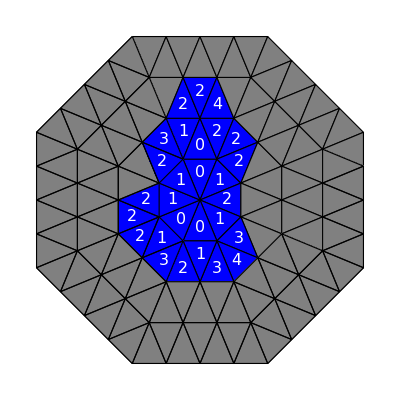

```mathematica
Graphics[displayBoard[board]]
```

```mathematica
res⟦flattenBoardIndex[{7,2,3},numOfRows]⟧
```

0.298435

```mathematica
boardifyFlatIndex[98,numOfRows]
```

{7,2,1}